```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CumDigDist[dflist_]:=Module[{df,cm},
df =Sort[dflist,#1[[1]]<#2[[1]]&];
cm =Sort[Flatten[Accumulate[Take[Sort[df, #1[[1]] > #2[[1]] &], {1, Length[df]}, {2, 2}]]], Greater];
Table[{df[[i]][[1]],cm[[i]]},{i,1,Length[df]}]
];
```

```mathematica
extractDgree[data_,j_,mindeg_, maxdeg_]:=Select[Table[{data[[i]][[1]],data[[i]][[j]]},{i,6,Length[data]}],And[#[[2]] >0,#[[1]]< maxdeg,#[[1]]≥ mindeg]&];
```

```mathematica
degFeq[list_]:=Map[{#⟦1⟧,#⟦2⟧/Total[list][[2]]}&,list];
```

```mathematica
MakeBins[list_,size_]:=Module[{k,bins,max,total},
k=1;
bins = {};
max = Max[Table[list[[i]][[1]],{i,Length[list]}]];
For[i=list[[1]][[1]], i< max,i=i+k,
total = Total[Select[list,And[#1[[1]] ≥ i,#1[[1]]< i+k]&]];
If[Length[total]==0,Continue[],];
bins =Append[bins,{i,total[[2]]/k}];
k=Floor[1+size*i -i];];
bins]
```

```mathematica
MakeBinsProb[list_,size_]:=Module[{k,bins,max,total,nodes},
k=1;
bins = {};
nodes = Total[list[[All,2]]];
max = Max[Table[list[[i]][[1]],{i,Length[list]}]];
For[i=list[[1]][[1]], i< max,i=i+k,
total = Total[Select[list,And[#1[[1]] ≥ i,#1[[1]]< i+k]&]];
If[Length[total]==0,Continue[],];
bins =Append[bins,{i,total[[2]]/k/nodes}];
k=Floor[1+size*i -i];];
bins]
```

```mathematica
FlateCum[list_,len_]:= Join[{list[[1]][[2]]},Flatten[Table[Table[{list[[j]][[2]]},{i,list[[j-1]][[1]]+1,list[[j]][[1]]}],{j,2,Min[Length[list],len]}]],ConstantArray[0,Max[0,len-list[[Length[list]]][[1]]]]]
```

```mathematica
ShowPowerInequal[file_]:=Module[{data,both, female, male,cboth,cfemale, cmale, fcboth, fcfemale, fcmale, maxlen,cumratio,cumratiobub},
 data = Import[file];
both = extractDgree[data,4,1,500];
female = extractDgree[data,2,1,500];
male = extractDgree[data,3,1,500];
cboth =CumDigDist[both];
cfemale =CumDigDist[female];
cmale =CumDigDist[male];
maxlen = cfemale[[Length[cfemale]]][[1]];
fcboth = FlateCum[cboth,maxlen];
fcfemale = FlateCum[cfemale,maxlen];
fcmale = FlateCum[cmale,maxlen];
cumratio =  Table[{cfemale[[i]][[1]],cfemale[[i]][[2]]/fcboth[[cfemale[[i]][[1]]]]},{i,1,Length[cfemale]}];
cumratiobub =  Table[{cfemale[[i]][[1]],cfemale[[i]][[2]]/fcboth[[cfemale[[i]][[1]]]],Power[female[[i]][[2]],0.25]},{i,1,Length[cfemale]}];
(*ListLogLinearPlot[cumratio,PlotRange-> {{1,maxlen+10},{0,0.3}},AxesOrigin->{1,0}]*)
BubbleChart[cumratiobub,ColorFunction -> Function[{x,y,r},Darker[Green,r/2]],BubbleSizes->{0.02,0.08},ChartElements->Graphics[Disk[]], ScalingFunctions->{"Log"},LabelingFunction-> None,FrameLabel->{"Degree (number of students + 1)","Precent of females from researchers with degree at least k"}, FrameTicks->{{Automatic,None},{Automatic,None}},AxesOrigin-> {0,0},PlotRange->{{-0.2,5},{0,0.25}}]]
```

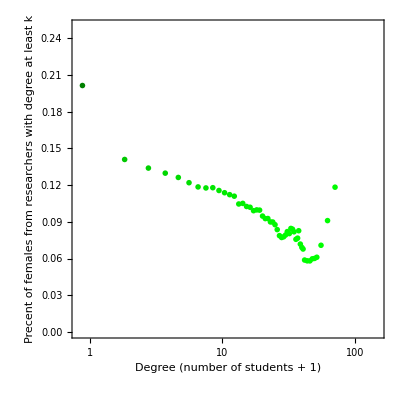

```mathematica
ShowPowerInequal["dblp_edges_maxAuthor20_mentee_frequent_known_degree_v1.csv"]
```

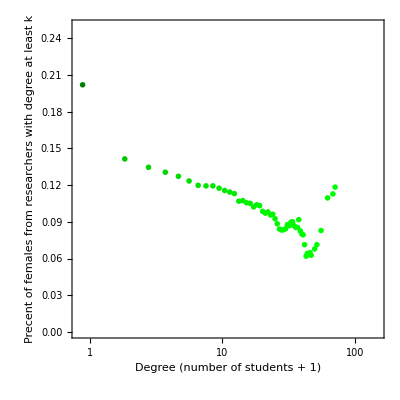

```mathematica
ShowPowerInequal["dblp_edges_maxAuthor20_mentee_frequent_known_degree_v0.csv"]
```

```mathematica
ShowDistNice[file_, mindeg_,maxdeg_,bin_]:=Module[{data,both, female, male,bcdf,fcdf, mcdf, bfit, ffit, mfit},
 data = Import[file];
both = extractDgree[data,4,mindeg,maxdeg];
female = extractDgree[data,2,mindeg,maxdeg];
male = extractDgree[data,3,mindeg,maxdeg];
bcdf = MakeBinsProb[both,bin]; (* CumDigDist[degFeq[both]]; *)
fcdf =MakeBinsProb[female,bin];(* CumDigDist[degFeq[female]]; *)
mcdf = MakeBinsProb[male,bin];(* CumDigDist[degFeq[male]]; *)
bfit = Fit[Log[bcdf],{1,x},x];
ffit = Fit[Log[fcdf],{1,x},x];
mfit = Fit[Log[mcdf],{1,x},x];
Show[ListLogLogPlot[{bcdf,fcdf,mcdf},PlotLegends->Placed[{"Both","Female", "Male"},{Left,Bottom}],PlotStyle->{Green,Red,Blue}], Plot[{bfit,ffit,mfit},{x,1,700},PlotStyle->{Green,Red,Blue},PlotLegends-> Placed[{"-β=" <> ToString[Round[bfit[[2]][[1]],.01]], "-β(R)=" <> ToString[Round[ffit[[2]][[1]],.01]],"-β(B)=" <> ToString[Round[mfit[[2]][[1]],.01]]},{Right,Top}]],Frame -> True, FrameLabel-> {"Degree", "Probability"}]]
```

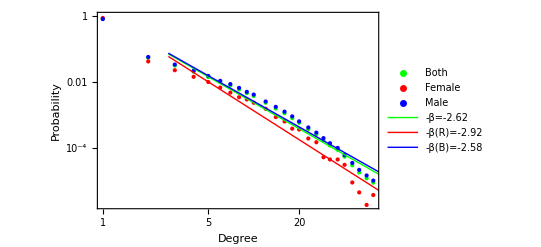

```mathematica
ShowDistNice["dblp_edges_maxAuthor20_mentee_frequent_known_degree_v1.csv",1,70,1.1]
```

```mathematica
ShowDistNice["dblp_edges_maxAuthor20_mentee_frequent_known_degree_v0.csv",1,70,1.1]
```

-Graphics-

```mathematica
data = Import["dblp_edges_maxAuthor20_mentee_frequent_known_degree_v1.csv"];
```

```mathematica
both = extractDgree[data,4,1,70];
```

```mathematica
female = extractDgree[data,2,1,70];
```

```mathematica
male = extractDgree[data,3,1,70];
```

```mathematica
bcdf = MakeBins[both,1.1]; 
fcdf =MakeBins[female,1.1];
mcdf = MakeBins[male,1.1];
```

```mathematica
bfit = Fit[Log[bcdf],{1,x},x]
ffit = Fit[Log[fcdf],{1,x},x]
mfit = Fit[Log[mcdf],{1,x},x]
```

12.9617-2.62059 x

11.5065-2.91636 x

12.7432-2.58424 x

```mathematica
extractDgreeZero[data_,j_,mindeg_, maxdeg_]:=Select[Table[{data[[i]][[1]],data[[i]][[j]]},{i,6,Length[data]}],And[#[[1]]< maxdeg,#[[1]]≥ mindeg]&];
```

```mathematica
ShowCumDistNice[file_, mindeg_,maxdeg_,bin_]:=Module[{data,both, female, male,bcdf,fcdf, mcdf, bfit, ffit, mfit},
 data = Import[file];
both = extractDgree[data,4,mindeg,maxdeg];
female = extractDgree[data,2,mindeg,maxdeg];
male = extractDgree[data,3,mindeg,maxdeg];
bcdf =CumDigDist[degFeq[both]]; 
fcdf =CumDigDist[degFeq[female]]; 
mcdf = CumDigDist[degFeq[male]]; 
bfit = Fit[Log[bcdf],{1,x},x];
ffit = Fit[Log[fcdf],{1,x},x];
mfit = Fit[Log[mcdf],{1,x},x];
Show[ListLogLogPlot[{bcdf,fcdf,mcdf},PlotLegends->Placed[{"Both","Female", "Male"},{Left,Bottom}],PlotStyle->{Green,Red,Blue}], Plot[{bfit,ffit,mfit},{x,1,700},PlotStyle->{Green,Red,Blue},PlotLegends-> Placed[{"-β=" <> ToString[Round[bfit[[2]][[1]]-1,.01]], "-β(R)=" <> ToString[Round[ffit[[2]][[1]]-1,.01]],"-β(B)=" <> ToString[Round[mfit[[2]][[1]]-1,.01]]},{Right,Top}]],Frame -> True, FrameLabel-> {"Degree", "Probabilty"}]]
```

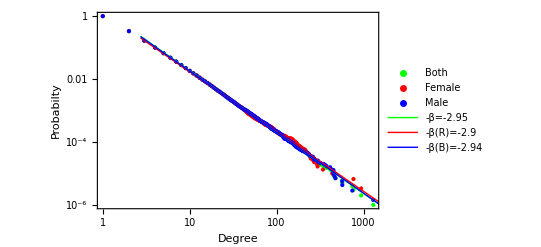

```mathematica
ShowCumDistNice["Bins_rho0_r0.3run999999.csv",0,1500,1]
```

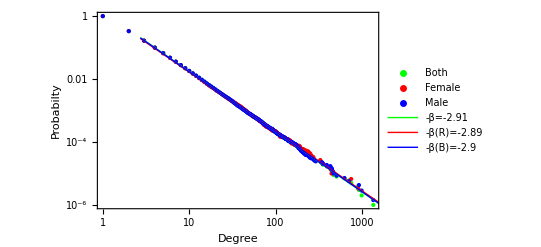

```mathematica
ShowCumDistNice["Bins_rho1_r0.3run999999.csv",0,1500,1]
```

```mathematica
ShowCumDistNice["Bins_rho0.7_r0.5run999999.csv",0,1500,1]
```

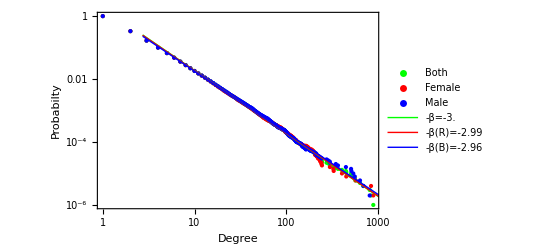

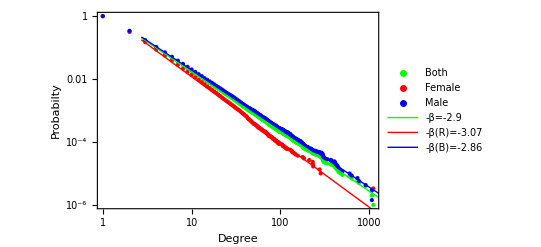

```mathematica
ShowCumDistNice["Bins_rho0.7_r0.3run999999.csv",0,1500,1]
```